```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];

enzModelsDir = "/home/mrama/Dropbox/MASSef/examples/"
mainDir=enzModelsDir<>"code_data/";
Import[mainDir<>"sim_plot_functions.m"];
Import[mainDir<>"simulation.m"];
```

/home/mrama/Dropbox/MASSef/examples/

## Build models

```mathematica
eqParams//TableForm
```

ssd | S05_fdp | S05_f6p | S05_pi | n_fdp | kcat_f | Keq
0 | 0.00007 | NA | NA | 2.05 | 5.7 | 41.5
0.00516074 | 0.0000699996 | 0.0000147181 | 0.504707 | 1.99987 | 5.7 | 41.5
0.00516146 | 0.0000699996 | 0.0411878 | 0.5 | 1.99986 | 5.7 | 41.5
0.00516202 | 0.0000699995 | 0.460663 | 0.488464 | 1.99986 | 5.7 | 41.5
0.00516221 | 0.0000699995 | 0.670757 | 0.000024598 | 1.99986 | 5.7 | 41.5
0.00516268 | 0.0000699992 | 0.501461 | 0.00969072 | 1.99985 | 5.7 | 41.5
0.00516283 | 0.0000699996 | 0.00074979 | 0.0378968 | 1.99987 | 5.7 | 41.5
0.00516298 | 0.0000699995 | 0.0110687 | 0.0387473 | 1.99984 | 5.69999 | 41.5
0.00516324 | 0.0000699992 | 0.000656024 | 0.599483 | 1.99985 | 5.7 | 41.5
0.0051633 | 0.0000699984 | 0.236085 | 1.46633×10^-10 | 1.99985 | 5.7 | 41.5
0.00516379 | 0.0000699944 | 0.000789145 | 0.493889 | 1.99983 | 5.7 | 41.5
0.00516382 | 0.000069995 | 0.501712 | 8.42495×10^-9 | 1.99983 | 5.69999 | 41.5002
0.00516385 | 0.0000699942 | 0.499999 | 0.0687214 | 1.99985 | 5.7 | 41.5
0.00516493 | 0.000069986 | 4.72799×10^-7 | 0.510984 | 1.99982 | 5.69999 | 41.5
0.00516493 | 0.0000699856 | 0.500387 | 0.0000251828 | 1.99984 | 5.69999 | 41.5006
0.00516505 | 0.0000699827 | 0.0688011 | 0.326776 | 1.99982 | 5.69999 | 41.4998
0.00516507 | 0.0000699833 | 0.00195616 | 0.000426705 | 1.99983 | 5.69999 | 41.4993
0.00516559 | 0.0000699807 | 0.0000962755 | 0.293162 | 1.99982 | 5.69998 | 41.5
0.00516584 | 0.0000699791 | 0.000152323 | 0.0906215 | 1.99981 | 5.69998 | 41.5
0.00516608 | 0.0000699804 | 0.501378 | 1.50124×10^-6 | 1.99982 | 5.69998 | 41.4982
0.00516674 | 0.0000699789 | 0.00334103 | 0.00172122 | 1.99982 | 5.69998 | 41.5
0.00516751 | 0.0000699784 | 3.98965×10^-7 | 0.505253 | 1.99981 | 5.69998 | 41.5002
0.00516849 | 0.0000699705 | 0.50377 | 3.87615×10^-6 | 1.99981 | 5.69986 | 41.5049
0.00517353 | 0.0000699896 | 0.0383589 | 0.518224 | 1.99972 | 5.69997 | 41.4969
0.00517635 | 0.000069952 | 0.00301238 | 0.499194 | 1.99971 | 5.69873 | 41.5226
0.00518468 | 0.0000699779 | 0.5 | 1.50817×10^-6 | 1.99963 | 5.69998 | 41.5002
0.00518991 | 0.0000699753 | 0.00933288 | 1.03668×10^-7 | 1.99957 | 5.69998 | 41.4994
0.00519078 | 0.0000699747 | 0.500023 | 0.0000805457 | 1.99956 | 5.69998 | 41.499
0.00524898 | 0.0000699756 | 0.601818 | 0.0000605947 | 1.99894 | 5.69994 | 41.4983
0.00534668 | 0.0000699739 | 0.644906 | 0.00104845 | 1.99793 | 5.69998 | 41.498
0.00537139 | 0.0000699769 | 0.705899 | 0.498978 | 1.99766 | 5.69992 | 41.4965
0.00544499 | 0.0000699809 | 0.00145843 | 0.499996 | 1.9969 | 5.69997 | 41.4977
0.00553018 | 0.0000699728 | 0.630536 | 1.5137×10^-7 | 1.99604 | 5.69997 | 41.4984
0.00554541 | 0.0000699708 | 0.00876697 | 0.5 | 1.99587 | 5.69997 | 41.4997
0.00556758 | 0.0000699673 | 0.608829 | 0.279228 | 1.99584 | 5.69997 | 41.4999
0.00558029 | 0.0000699675 | 0.592365 | 0.0125189 | 1.99541 | 5.69996 | 41.4964
0.00559926 | 0.0000699682 | 0.00136278 | 0.000133317 | 1.99533 | 5.69994 | 41.5004
0.00559975 | 0.0000699661 | 0.000453752 | 0.150113 | 1.99514 | 5.70033 | 41.5013
0.00560218 | 0.0000699636 | 0.482745 | 1.21482×10^-7 | 1.99517 | 5.69997 | 41.4988
0.00562166 | 0.0000699633 | 0.0000293998 | 0.500071 | 1.99458 | 5.69994 | 41.4961
0.0056324 | 0.0000699613 | 0.0748575 | 0.468439 | 1.99497 | 5.69994 | 41.4967
0.0056606 | 0.0000699612 | 0.648558 | 0.0000262177 | 1.99459 | 5.69996 | 41.4989
0.00566853 | 0.0000699607 | 2.6841×10^-7 | 0.5 | 1.99462 | 5.69994 | 41.4968
0.00566936 | 0.0000699615 | 0.498443 | 0.0562231 | 1.99459 | 5.69996 | 41.4972
0.00567585 | 0.0000699605 | 0.5 | 1.54223×10^-8 | 1.99456 | 5.69996 | 41.4971
0.00568097 | 0.0000699572 | 0.00024032 | 0.530648 | 1.99458 | 5.69996 | 41.4977
0.00569653 | 0.0000699559 | 0.00182075 | 2.66846×10^-6 | 1.99434 | 5.69995 | 41.495
0.0057099 | 0.0000699572 | 0.500041 | 2.55297×10^-6 | 1.99421 | 5.69992 | 41.4951
0.00571102 | 0.0000699551 | 0.666939 | 0.000203988 | 1.99418 | 5.69996 | 41.4969
0.00575456 | 0.000069954 | 0.0145382 | 0.235236 | 1.99377 | 5.69995 | 41.4971
0.00577343 | 0.0000699536 | 0.5 | 6.7729×10^-9 | 1.99354 | 5.69996 | 41.4983
0.00578069 | 0.0000699529 | 0.521206 | 0.373932 | 1.9935 | 5.69996 | 41.4972
0.00580663 | 0.0000699516 | 0.0348997 | 1.23351×10^-9 | 1.99319 | 5.69996 | 41.4969
0.00581515 | 0.0000699511 | 0.158424 | 2.26467×10^-7 | 1.99316 | 5.69996 | 41.497
0.00585605 | 0.0000699545 | 0.0344783 | 0.0000117718 | 1.99267 | 5.69995 | 41.4956
0.00587699 | 0.0000699485 | 0.000663835 | 1.04394×10^-8 | 1.99247 | 5.69995 | 41.4984
0.00590984 | 0.0000699486 | 0.000220324 | 0.0000189642 | 1.99222 | 5.69995 | 41.4967
0.00593038 | 0.0000699469 | 0.61137 | 2.92774×10^-6 | 1.99203 | 5.70005 | 41.4966
0.00593462 | 0.000069945 | 0.0135714 | 0.416147 | 1.99198 | 5.69995 | 41.4967
0.00595526 | 0.0000699417 | 0.00041124 | 0.000168991 | 1.99178 | 5.69996 | 41.5049
0.00596856 | 0.000069945 | 0.0097 | 0.498713 | 1.99165 | 5.69995 | 41.4958
0.00597299 | 0.0000699439 | 0.0013655 | 1.18074×10^-9 | 1.99161 | 5.69995 | 41.4956
0.00597422 | 0.0000699432 | 0.305191 | 2.40638×10^-7 | 1.9916 | 5.69995 | 41.4979
0.00598606 | 0.0000699426 | 0.55894 | 0.000724048 | 1.99148 | 5.69995 | 41.4964
0.00600303 | 0.0000699409 | 0.501285 | 0.000168244 | 1.99126 | 5.69995 | 41.4954
0.00601148 | 0.000069941 | 2.27095×10^-6 | 0.0815556 | 1.99123 | 5.69995 | 41.4958
0.00602148 | 0.0000699403 | 0.0000983911 | 0.502463 | 1.99113 | 5.69995 | 41.497
0.00603293 | 0.0000699397 | 3.27808×10^-7 | 0.5 | 1.99102 | 5.69994 | 41.4964
0.00611083 | 0.0000699387 | 0.500108 | 9.35304×10^-6 | 1.99018 | 5.69994 | 41.4972
0.00612907 | 0.0000699369 | 0.00304224 | 0.0550897 | 1.99008 | 5.69994 | 41.4966
0.00613934 | 0.000069936 | 0.653388 | 3.81378×10^-7 | 1.99 | 5.69994 | 41.4977
0.0061668 | 0.0000699354 | 0.0410556 | 0.412369 | 1.98973 | 5.69994 | 41.4961
0.00618508 | 0.0000699351 | 0.572736 | 0.000026893 | 1.98956 | 5.69994 | 41.4964
0.00619266 | 0.0000699302 | 0.372657 | 0.437313 | 1.98948 | 5.69995 | 41.5052
0.00623074 | 0.0000699304 | 0.564364 | 0.483921 | 1.98912 | 5.69994 | 41.5039
0.00623994 | 0.0000699281 | 0.111282 | 0.000268731 | 1.98903 | 5.69993 | 41.4942
0.00626146 | 0.0000699276 | 0.505774 | 0.000858878 | 1.98873 | 5.69993 | 41.4936
0.0062883 | 0.0000699267 | 0.000582892 | 3.46885×10^-7 | 1.98857 | 5.69993 | 41.4968
0.00628943 | 0.0000699314 | 0.00630919 | 0.516001 | 1.98856 | 5.69991 | 41.4903
0.00632732 | 0.000069926 | 0.507065 | 6.15366×10^-8 | 1.9882 | 5.69992 | 41.4938
0.0065049 | 0.0000699209 | 0.00381018 | 1.00957×10^-7 | 1.98654 | 5.69992 | 41.4942
0.00650756 | 0.0000699088 | 0.499878 | 0.5 | 1.98648 | 5.69985 | 41.4976
0.00652301 | 0.0000699062 | 0.00144819 | 1.04524×10^-9 | 1.98621 | 5.6999 | 41.4886
0.00668876 | 0.0000698959 | 0.0943644 | 0.0156021 | 1.98483 | 5.69989 | 41.4932
0.00688552 | 0.0000698842 | 0.48089 | 0.000100978 | 1.9829 | 5.69987 | 41.4995
0.00707294 | 0.0000698834 | 0.12297 | 2.607×10^-9 | 1.98141 | 5.69987 | 41.4929
0.00724397 | 0.0000698499 | 0.660134 | 2.9507×10^-7 | 1.97961 | 5.69984 | 41.5099
0.00749589 | 0.0000699165 | 3.84005×10^-7 | 8.84804×10^-7 | 1.97753 | 5.70271 | 41.4511
0.00808596 | 0.000069817 | 0.499694 | 4.13605×10^-6 | 1.97228 | 5.69973 | 41.4899
0.00810072 | 0.0000698039 | 0.00185766 | 1.89577×10^-6 | 1.97254 | 5.6997 | 41.4889
0.0085778 | 0.0000697901 | 0.00811626 | 1.87906×10^-6 | 1.96843 | 5.69972 | 41.4914
0.00880135 | 0.0000697485 | 0.0000507514 | 2.90272×10^-8 | 1.96689 | 5.69957 | 41.4853
0.00898808 | 0.0000697032 | 0.706978 | 2.53103×10^-8 | 1.96535 | 5.69944 | 41.4852
0.00936972 | 0.0000696704 | 3.44411×10^-6 | 2.99148×10^-9 | 1.96248 | 5.69928 | 41.4602
0.00988013 | 0.000069511 | 0.158206 | 0.000139353 | 1.95849 | 5.6987 | 41.4601
0.0140911 | 0.0000700201 | 2.23964×10^-10 | 0.0000100652 | 1.93068 | 5.6998 | 41.5
1.8681 | 0.0000700199 | 0.156531 | 2.62072×10^-9 | 1.0378 | 5.69978 | 41.4998
2.10683 | 0.0000700199 | 3.62931×10^-8 | 6.92506×10^-11 | 1.00011 | 5.69981 | 41.5
2.10685 | 0.0000700197 | 4.6586×10^-7 | 3.18604×10^-11 | 1.00011 | 5.69979 | 41.5
415.656 | 0.426583 | 0.703108 | 2.75046×10^-8 | 1.70845 | 4.83993×10^-6 | 2.24224
450.372 | 0.503687 | 0.689595 | 0.69479 | 1.75245 | 8.41454×10^-9 | 41.4976

```mathematica
baseDir =enzModelsDir<> "FBP2/fit_FBP2/output/";
ssdThreshold=0.1;
baseModel=constructModel[{Overscript[fdp^c->f6p^c+pi^c, FBP2]}];
updateCustomRateLaws[baseModel, {Subscript[v, FBP2]->((FBP2^)_^ kcat_f_ (fdp^c[t])^nH_)/(S05_fdp_^nH_+(fdp^c[t])^nH_)}];

inputDir = baseDir<>"model_simulations/models/";
If[!DirectoryQ[inputDir],
	CreateDirectory[inputDir,CreateIntermediateDirectories-> True]
];


nModelEnsembles = 3;
Do[
eqParams = Import[baseDir <> "treated_data/predicted_params_distribution_new_lma_"<>ToString@modelEnsembleI<>"_log_ssd_predS05.csv", "CSV"];

eMASSModelList=Import[baseDir<>"model_simulations/models/model_FBP2_all_100_"<>ToString@modelEnsembleI<>".mx"];

modelList={};

Do[
If[eqParams[[modelI,1]]< ssdThreshold && modelI < (Length@eMASSModelList+3),

model = baseModel;

metInitialConc = FilterRules[eMASSModelList[[modelI-2]]["InitialConditions"],baseModel["Species"]];
metInitialConc=Map[Keys@# -> Values@#&, metInitialConc];
updateInitialConditions[model,metInitialConc];

paramList={ S05_fdp_-> eqParams[[modelI,2]],S05_f6p_->eqParams[[modelI,3]], S05_pi_->eqParams[[modelI,4]], nH_-> eqParams[[modelI,5]], kcat_f_-> eqParams[[modelI,6]],  Underscript[Volume, c]-> 1, (FBP2^)_^->9.72*10^-8 };
updateParameters[model, paramList];

AppendTo[modelList,model],

Break[]],

{modelI, 3,Length@eqParams}]; 

Export[inputDir<>"model_FBP2_hill_irrev_100_"<>ToString@modelEnsembleI<>".mx",modelList, "MX"];,

{modelEnsembleI, 1, nModelEnsembles}];
```

```mathematica
Length@modelList
```

95

## Hill simulations

```mathematica
getFirstHillModelData[modelI_, resWorking_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_, indMet_, tValues_]:=
	Block[{simConcEnz, simConcMets, simFlux},

	simConcMets=Join[{Flatten@{"t", headerConcMets}},
					Table[
						Flatten[{tVal, Flatten@{Values@{resWorking[[modelI, 1]][[indMet]]}} /. t-> tVal}], 
					{tVal,tValues}]];
		
	simFlux=Join[{Flatten@{"t", headerFlux}},
				Table[
					Flatten[{tVal, Flatten@{Values@resWorking[[modelI, 2]]} /. t-> tVal}], 
				{tVal,tValues}]];

	Return[{{}, simConcMets, simFlux}];
];
```

```mathematica
getHillModelData[modelI_, resWorking_, simConcEnz_, simConcMets_, simFlux_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_,  indMet_, tValues_]:=
	Block[{simConcEnzLocal, simConcMetsLocal, simFluxLocal, simConcEnzTemp, simConcMetsTemp, simFluxTemp},

						
	simConcMetsTemp=Join[{Flatten@{"t",headerConcMets}},
						Table[
							Flatten[{tVal, Flatten@{Values@{resWorking[[modelI, 1]][[indMet]]}}/.t-> tVal}],
						{tVal,tValues}]];
	
	simFluxTemp=Join[{Flatten@{"t",headerFlux}},
					Table[
						Flatten[{tVal,Flatten@{Values@resWorking[[modelI, 2]]}/.t-> tVal}],
					{tVal,tValues}]];
	
	
	simConcMetsLocal = MapThread[Flatten[{#1,#2}]&, {simConcMets,simConcMetsTemp}];
	simFluxLocal = MapThread[Flatten[{#1,#2}]&, {simFlux,simFluxTemp}];

	Return[{{},simConcMetsLocal, simFluxLocal}];
];
```

```mathematica
simulateHillEnsembleNoCheck[inputDir_, outputDir_, enzName_, modelID_, nModelEnsembles_, tFinal_, tValues_, 
				initCondList_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_, subInd_, prodInd_, KeqVal_:""]:=
	Block[{KeqData, prods, subs, indMet, modelList,
			metsList, res, resWorking, modelI, simConcEnz, simConcMets, simFlux, simConcEnzTemp, simConcMetsTemp, 
			simFluxTemp},
	 
	indMet = Flatten[{subInd, prodInd}];

	Do[

		modelList = Import[inputDir <> "model_" <> enzName <> "_" <> modelID <> "_" <> ToString[modelEnsembleI] <> ".mx"];
		Print[inputDir <> "model_" <> enzName <> "_" <> modelID <> "_" <> ToString[modelEnsembleI] <> ".mx"];
		res = Map[TimeConstrained[simulate[modelList[[#]], {t, 0, tFinal}, InitialConditions -> initCondList, MaxSteps-> Infinity], 30, "err"]&, Range[1, Length@modelList]];
		resWorking = Delete[res, Position[res,"err"]];	

		modelI=1;
				
		{simConcEnz, simConcMets, simFlux} = getFirstHillModelData[modelI, resWorking, headerConcEnz, headerConcMets, headerFlux, indEnz, indMet, tValues];
		
		Do[ (* go through individual models *)
			
				
			{simConcEnz, simConcMets, simFlux} = getHillModelData[modelI, resWorking, simConcEnz, simConcMets, 
							simFlux, headerConcEnz, headerConcMets, headerFlux, indEnz, indMet, tValues];,
	
		{modelI, 2, Length@resWorking}];

		Export[outputDir <> "/sim_res_conc_mets_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <>ToString[KeqVal] <> ".csv", simConcMets, "TSV"];
		Export[outputDir <> "/sim_res_flux_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <>ToString[KeqVal] <> ".csv", simFlux, "TSV"];

		Export[outputDir<> "/data_mx/sim_res_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <> ToString[KeqVal] <> ".mx", resWorking, "MX"];,

	{modelEnsembleI, nModelEnsembles[[1]], nModelEnsembles[[2]]}];
	
	
];
```

## Simulations

```mathematica
modelList=Import[inputDir<>"model_FBP2_hill_irrev_1000_"<>ToString@0<>".mx", "MX"];
```

```mathematica
Do[
tFinal=5*10^12;
Print[modelI];
{conc,flux}=simulate[modelList[[modelI]],{t,0,tFinal}];,
{modelI, 1, Length@modelList}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

14

15

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

16

17

18

19

20

21

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

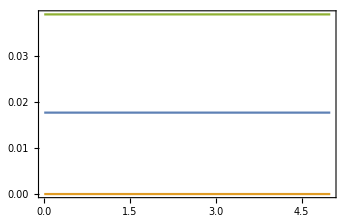

```mathematica
plotSimulation[conc,{t,0,tFinal}, PlotFunction-> Plot]
```

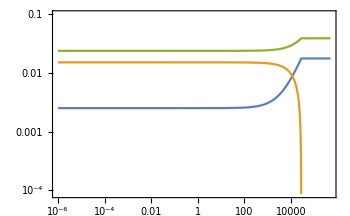

```mathematica
tFinal=5*10^5;
{conc,flux}=simulate[modelList[[1]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}, PlotRange-> {{0,tFinal},{0.,0.1}}]
```

```mathematica
modelList[[9300]]["Parameters"]
```

{S05_fdp_→0.0000696091,S05_f6p_→509107.,S05_pi_→0.781854,nH_→1.91334,kcat_FBP2→5.6992,K_FBP2→41.4844,Volume_c→1,(FBP2^)_^→9.72×10^-8}

### Systematic simulations

```mathematica
enzName="FBP2";

outputDirBase = baseDir<>"model_simulations/data/";
If[!DirectoryQ[outputDirBase],
	CreateDirectory[outputDirBase,CreateIntermediateDirectories-> True]
];



headerConcMets={"fdp","f6p",  "pi"};
headerFlux={"v_1"};
subInd = {2};
prodInd={1,3};
indEnz={};

initCondList={};
outputDirList={"noPerturb"};


tValues=Map[10^#&,Range[-6,3, 0.1]];
tFinal=1000;
tValues=Insert[tValues,0., 1];


modelIDList={"hill_irrev_100"};
nModelEnsembles={1,3};


outputDir =outputDirBase;
If[!DirectoryQ[outputDir<>"/data_mx/"],
	CreateDirectory[outputDir<>"/data_mx/",CreateIntermediateDirectories-> True]
];
```

```mathematica
headerConcEnz={};
```

```mathematica
Do[

simulateHillEnsembleNoCheck[inputDir, outputDir, enzName, modelID, nModelEnsembles, tFinal, tValues, initCondList, headerConcEnz, headerConcMets, headerFlux, indEnz,subInd, prodInd];,


{modelID, modelIDList}];
```

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_hill_irrev_100_1.mx

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_hill_irrev_100_2.mx

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_hill_irrev_100_3.mx